```mathematica
(* Results for experiment H-1 *)
```

```mathematica
Get["H1.m"];
eV=1/27.2117;
h1all={#[[1]],#[[2]]*eV}&/@propertylist;
h1good=Select[h1all,#[[1]]≥-0.9&];
h11s=Select[h1all,#[[1]]≥-1.0&];
h12s=Select[h1all,#[[1]]<=-1.0&];
```

```mathematica
h1fit=Fit[h1good,{1,q,q^2},q]
h1sfit=Fit[h11s,{1,q,q^2},q]
h2sfit=Fit[h12s,{1,(q+1),(q+1)^2},q]
h1f=Interpolation[h1all];
```

-0.437825+0.21723 q+0.217969 q^2

-0.437579+0.217653 q+0.216724 q^2

-0.440164-0.74049 (1+q)+0.189213 (1+q)^2

```mathematica
h1f[-1]
```

-0.440921

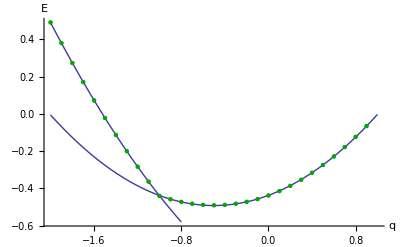

```mathematica
res3=Show[ListPlot[h1all,PlotStyle->Darker[Green]],Plot[h1sfit,{q,-2,1}],Plot[h2sfit,{q,-2,-.8}],ListPlot[h1all,PlotStyle->Darker[Green]],AxesLabel->{q,Ε}]
```

```mathematica
Export["/home/avery/work/diku/Ph.D./dftfem/H-sanity/H1-1s-2s.pdf",res3];
```

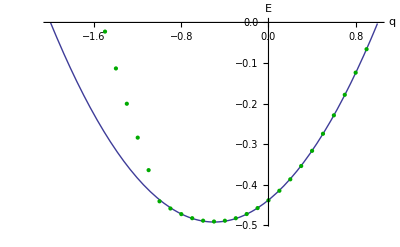

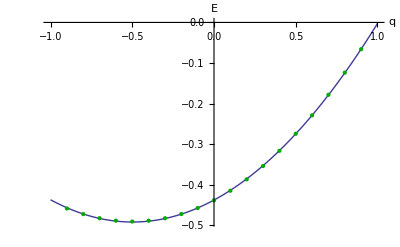

```mathematica
res1=Show[Plot[h1fit,{q,-2,1}],ListPlot[h1all,PlotStyle->Darker[Green]],AxesLabel->{q,Ε}]
res2=Show[Plot[h1fit,{q,-1,1}],ListPlot[h1good,PlotStyle->Darker[Green]],AxesLabel->{q,Ε}]
```

```mathematica
Export["H1-bad.pdf",res1];
Export["H1-good.pdf",res2];
```

```mathematica
Evc[q_]:=Evaluate[h1f[q]]
Evcfit[qq_]:=Evaluate[h1fit/.q->qq]
h1err={#[[1]],((h1fit/.q->#[[1]])-#[[2]])}&/@h1good;
```

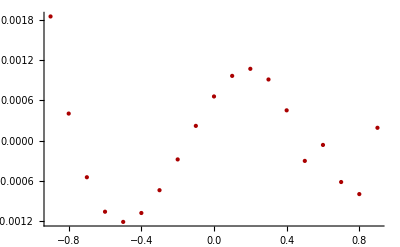

```mathematica
h1errplot=ListPlot[h1err,PlotStyle->Darker[Red]]
```

```mathematica
Export["H1-errplot.pdf",h1errplot];
```

```mathematica
zeroerr=Evcfit[0]+11.9318/27.2117
```

0.000655494

```mathematica
(*Results for experiment H-2*)
Get["H2.m"];
h2f=Interpolation[propertylist,InterpolationOrder->2];
E2[Δx_,q_]:=h2f[q,Δx]*eV;
E2f[Δx_,q_]:=Evcfit[q]-1/2*.5^2/(2*Δx);
```

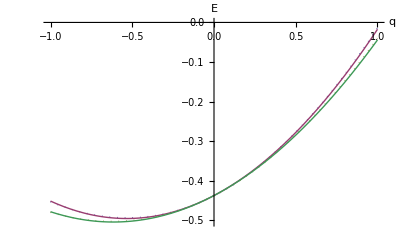

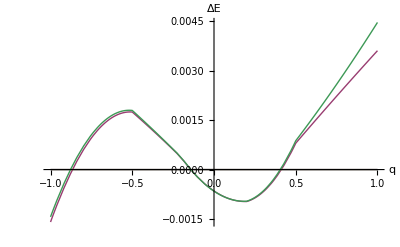

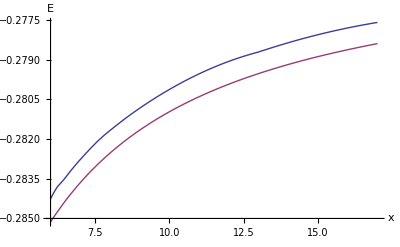

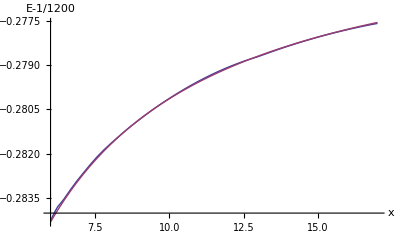

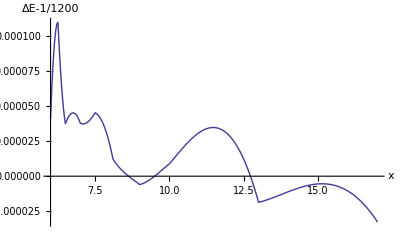

```mathematica
res1=Plot[{E2[17,q],Evcfit[q]-1/2*q^2/(2*17),E2[6,q],Evcfit[q]-1/2*q^2/(2*6)},{q,-1,1},AxesLabel->{q,Ε},PlotStyle->{{Dotted,Thick},Thick}]
Plot[{0,E2[17,q]-(Evcfit[q]-1/2*q^2/(2*17)),0,E2[6,q]-(Evcfit[q]-1/2*q^2/(2*6))},{q,-1,1},AxesLabel->{q,ΔΕ}]
Plot[{E2[x,.5],(Evcfit[.5]-1/2*.5^2/(2*x))},{x,6,17},AxesLabel->{x,Ε}]
Plot[{E2[x,.5],(Evcfit[.5]-1/2*.5^2/(2*x)+1/1200)},{x,6,17},AxesLabel->{x,Ε-1/1200}]
Plot[{E2[x,.5]-(Evcfit[.5]-1/2*.5^2/(2*x)+1/1200)},{x,6,17},AxesLabel->{x,ΔΕ-1/1200}]
```

```mathematica
1/1200.
```

0.000833333

```mathematica
(* Results for experiment H-3 *)
Get["H3e.m"];
h3et={#[[1,1]],#[[1,2]],#[[1,3]],#[[2]]*eV}&/@propertylist;
h3ef=Interpolation[{#[[1]],#[[2]]*eV}&/@propertylist,InterpolationOrder->{2,2,1}];
E3e[Δx_,q_,ϵ_]:=h3ef[q,Δx,ϵ];
Get["H3q.m"];
h3qt={#[[1,1]],#[[1,2]],#[[1,3]],#[[2]]*eV}&/@propertylist;
h3qf=Interpolation[{#[[1]],#[[2]]*eV}&/@propertylist,InterpolationOrder->{2,2,1}];
E3q[Δx_,q_,ϵ_]:=h3qf[q,Δx,ϵ];
Get["H3x.m"];
h3xt={#[[1,1]],#[[1,2]],#[[1,3]],#[[2]]*eV}&/@propertylist;
h3xf=Interpolation[{#[[1]],#[[2]]*eV}&/@propertylist,InterpolationOrder->{2,2,1}];
E3x[Δx_,q_,ϵ_]:=h3xf[q,Δx,ϵ];

α[ϵ_]:=-(1-ϵ)/(1+ϵ);
E3f[Δx_,q_,ϵ_]:=Evc[q]-α[ϵ]/2*q^2/(2*Δx);
E3fit[Δx_,q_,ϵ_]:=Evcfit[q]-α[ϵ]/2*q^2/(2*Δx);
```

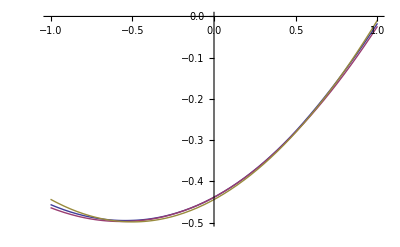

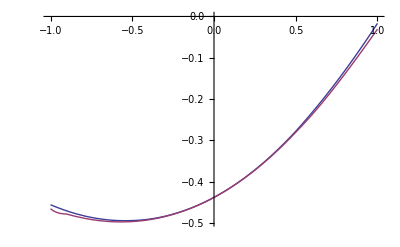

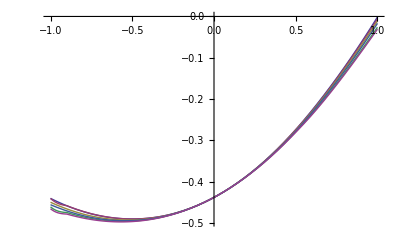

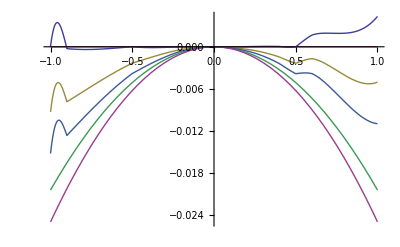

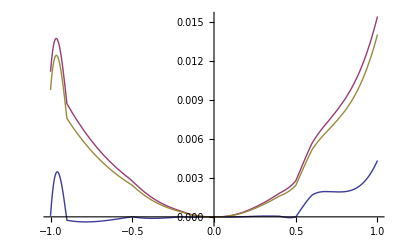

```mathematica
Plot[{E3q[10,q,10000],E2[10,q],E2f[10,q]},{q,-1,1}]
Plot[{E3q[10,q,10000],E3f[10,q,10000]},{q,-1,1}]
Plot[{E3q[10,q,1],E3f[10,q,1],E3q[10,q,10],E3f[10,q,10],E3q[10,q,10000],E3f[10,q,10000]},{q,-1,1}]
Plot[{E3q[10,q,1]-Evc[q],E3f[10,q,1]-Evc[q],E3q[10,q,10]-Evc[q],E3f[10,q,10]-Evc[q],E3q[10,q,10000]-Evc[q],E3f[10,q,10000]-Evc[q]},{q,-1,1}]
Plot[{E3q[10,q,1]-E3f[10,q,1],E3q[10,q,10]-E3f[10,q,10],E3q[10,q,10000]-E3f[10,q,10000]},{q,-1,1}]
```

```mathematica
α[10000.]
```

0.9998

```mathematica
h3ef[0,1,1]
```

{3,3,3}[0,1,1]

{3,3,3}

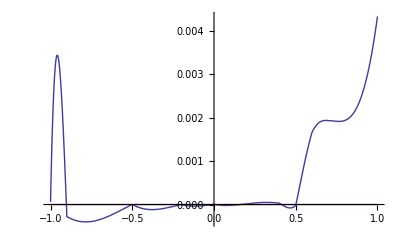

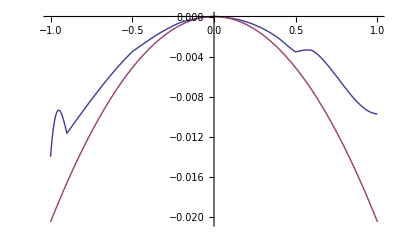

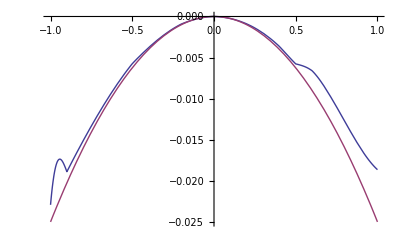

```mathematica
Plot[{E3q[7,q,1]-Evc[q],E3f[10,q,1]-Evc[q]},{q,-1,1},PlotRange->All,Axes->{False,True}]
Plot[{E3q[7,q,10]-Evc[q],E3f[10,q,10]-Evc[q]},{q,-1,1},PlotRange->All,Axes->{True,True}]
Plot[{E3q[7,q,10000]-Evc[q],E3f[10,q,10000]-Evc[q]},{q,-1,1},PlotRange->All,Axes->{True,True}]
```

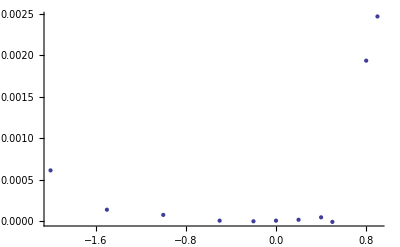

```mathematica
ListPlot[{#[[1]],#[[4]]-Evc[#[[1]]]}&/@Select[h3qt,#[[3]]==1&&#[[2]]==10&],PlotRange->All,Axes->{False,True}]
```

```mathematica
h3qt[[1]]
```

{0.,10.,10000.,-0.438473}